```mathematica
(*定义目标文件夹路径*)
targetFolder="DuallineSimulation";
If[SameQ[$OperatingSystem,"Windows"],basePath=FileNameJoin[{$HomeDirectory,"Desktop",targetFolder}]<>"\\",basePath=FileNameJoin[{$HomeDirectory,"Desktop",targetFolder}]<>"/"]
```

C:\Users\fengw\Desktop\DuallineSimulation\

```mathematica
(*设置样本大小*)
Nmcmc=70;
```

```mathematica
(*初始化结果列表，根据前面的计算，不再计算1b和1c波形*)
SNRCountsUniform=Table[{},{Nmcmc},{4}];
newSNRListsUniform=Table[{},{Nmcmc},{4}]; 
ΔI3toI3ListUniform=Table[{},{Nmcmc}];

SNRCountsLogUniform=Table[{},{Nmcmc},{4}];
newSNRListsLogUniform=Table[{},{Nmcmc},{4}]; 
ΔI3toI3ListLogUniform=Table[{},{Nmcmc}];
```

```mathematica
(*定义一个函数以提取和统计大于7的元素*)
processList[list_]:=Module[{filteredList},filteredList=Select[list,#>7&];
Length[filteredList]]

processSimulation[samplingType_]:=Module[{},
Do[start=AbsoluteTime[];
SamplingType=samplingType;(*Determine NS characteristic parameters' lists based on sampling type*)
Get[basePath<>"NSWaveformsDNSalpha10.m"];
(*根据采样类型选择正确的列表*)
Switch[samplingType,
"Uniform",(*更新Uniform列表*)
SNRCountsUniform[[j,1]]=processList[snrH1aList];
newSNRListsUniform[[j,1]]=Select[snrH1aList,#>7&];
SNRCountsUniform[[j,2]]=processList[snrH2aList];
newSNRListsUniform[[j,2]]=Select[snrH2aList,#>7&];
SNRCountsUniform[[j,3]]=processList[snrH2bList];
newSNRListsUniform[[j,3]]=Select[snrH2bList,#>7&];
SNRCountsUniform[[j,4]]=processList[snrH2cList];
newSNRListsUniform[[j,4]]=Select[snrH2cList,#>7&];
ΔI3toI3ListUniform[[j]]=ΔI3toI3,

"LogUniform",(*更新LogUniform列表*)
SNRCountsLogUniform[[j,1]]=processList[snrH1aList];
newSNRListsLogUniform[[j,1]]=Select[snrH1aList,#>7&];
SNRCountsLogUniform[[j,2]]=processList[snrH2aList];
newSNRListsLogUniform[[j,2]]=Select[snrH2aList,#>7&];
SNRCountsLogUniform[[j,3]]=processList[snrH2bList];
newSNRListsLogUniform[[j,3]]=Select[snrH2bList,#>7&];
SNRCountsLogUniform[[j,4]]=processList[snrH2cList];
newSNRListsLogUniform[[j,4]]=Select[snrH2cList,#>7&];
ΔI3toI3ListLogUniform[[j]]=ΔI3toI3];
end=AbsoluteTime[];
elapsedTime=end-start;
Print["",j," simulation time: ",elapsedTime];,{j,1,Nmcmc}]]
```

```mathematica
(*calculate and save data*)
processSimulation["Uniform"];  
mergedSNRCountsUniform=Transpose[SNRCountsUniform][[Range[4]]];
Export[basePath <> "mergedSNRCountsUniform.txt",mergedSNRCountsUniform,"Table"];
```

1 simulation time: 289.810336

2 simulation time: 274.127444

3 simulation time: 273.243064

4 simulation time: 272.887311

5 simulation time: 272.351977

6 simulation time: 273.409178

7 simulation time: 273.352784

8 simulation time: 273.20309

9 simulation time: 272.545182

10 simulation time: 274.051905

11 simulation time: 273.669746

12 simulation time: 273.367277

13 simulation time: 274.897752

14 simulation time: 275.915216

15 simulation time: 273.594457

16 simulation time: 273.755025

17 simulation time: 273.345198

18 simulation time: 272.148847

19 simulation time: 272.331275

General::munfl: 0.683992 1.6169593×10^-29283739 太小，不适合被表示为归一化机器数；可能无法保持原来的精度.

20 simulation time: 271.216362

21 simulation time: 273.292224

22 simulation time: 273.45634

23 simulation time: 273.277036

24 simulation time: 274.087175

25 simulation time: 273.643219

26 simulation time: 273.580029

27 simulation time: 273.130294

28 simulation time: 272.739268

29 simulation time: 273.357835

30 simulation time: 277.696663

31 simulation time: 275.200083

32 simulation time: 270.545198

33 simulation time: 270.728043

34 simulation time: 269.954968

35 simulation time: 271.193475

36 simulation time: 270.630537

37 simulation time: 271.28552

38 simulation time: 271.902696

39 simulation time: 270.619987

40 simulation time: 271.354879

41 simulation time: 270.284654

42 simulation time: 270.71811

43 simulation time: 270.813331

44 simulation time: 270.964175

45 simulation time: 270.299732

46 simulation time: 271.601832

47 simulation time: 271.132515

48 simulation time: 271.748558

49 simulation time: 274.698912

50 simulation time: 272.085386

51 simulation time: 271.454585

52 simulation time: 271.439017

53 simulation time: 271.563524

54 simulation time: 271.761791

55 simulation time: 270.944695

56 simulation time: 271.194157

57 simulation time: 272.1458

58 simulation time: 272.182809

59 simulation time: 271.587036

60 simulation time: 271.459043

61 simulation time: 272.522967

62 simulation time: 272.109381

63 simulation time: 271.86861

64 simulation time: 271.388242

65 simulation time: 271.548437

66 simulation time: 270.998777

67 simulation time: 270.538126

68 simulation time: 271.849625

69 simulation time: 271.615469

70 simulation time: 271.578757

```mathematica
(*calculate and save data*)
processSimulation["LogUniform"];  
mergedSNRCountsLogUniform=Transpose[SNRCountsLogUniform][[Range[4]]];
Export[basePath <> "mergedSNRCountsLogUniform.txt",mergedSNRCountsLogUniform,"Table"];
```

1 simulation time: 271.809367

2 simulation time: 271.735879

3 simulation time: 269.817467

4 simulation time: 271.01392

5 simulation time: 271.430998

6 simulation time: 271.463903

7 simulation time: 271.791466

8 simulation time: 271.371775

9 simulation time: 271.059027

10 simulation time: 270.173985

11 simulation time: 270.88085

12 simulation time: 271.859749

13 simulation time: 271.311007

14 simulation time: 271.490067

15 simulation time: 270.74551

16 simulation time: 269.578596

17 simulation time: 270.72956

18 simulation time: 271.354439

19 simulation time: 272.157251

20 simulation time: 270.995883

21 simulation time: 270.800832

22 simulation time: 271.244718

23 simulation time: 271.449236

24 simulation time: 271.909016

25 simulation time: 271.804642

26 simulation time: 272.096059

27 simulation time: 270.995808

28 simulation time: 270.955249

29 simulation time: 270.530105

30 simulation time: 270.172043

31 simulation time: 271.075665

32 simulation time: 271.521471

33 simulation time: 271.708144

34 simulation time: 271.889977

35 simulation time: 271.51067

36 simulation time: 270.665628

37 simulation time: 270.945254

38 simulation time: 271.022372

39 simulation time: 271.982731

40 simulation time: 271.506525

41 simulation time: 271.674604

42 simulation time: 271.785453

43 simulation time: 273.045937

44 simulation time: 271.838105

45 simulation time: 271.081396

46 simulation time: 272.003155

47 simulation time: 270.528748

48 simulation time: 271.652619

49 simulation time: 270.863143

50 simulation time: 271.913695

51 simulation time: 271.651292

52 simulation time: 271.71943

53 simulation time: 270.56211

General::munfl: 0.570738 8.9414007×10^-7252258 太小，不适合被表示为归一化机器数；可能无法保持原来的精度.

54 simulation time: 267.481875

55 simulation time: 272.74521

56 simulation time: 271.294158

57 simulation time: 271.269612

58 simulation time: 270.742346

59 simulation time: 271.385136

60 simulation time: 273.170698

61 simulation time: 270.154169

62 simulation time: 271.712827

63 simulation time: 271.839686

64 simulation time: 271.787825

65 simulation time: 271.897625

66 simulation time: 270.864978

67 simulation time: 271.786262

68 simulation time: 272.524578

69 simulation time: 271.59399

70 simulation time: 271.326756

```mathematica
(*import data using calculated results*)
mergedSNRCountsUniform=Import[basePath <> "mergedSNRCountsUniform.txt","Table"];
mergedSNRCountsLogUniform=Import[basePath <> "mergedSNRCountsLogUniform.txt","Table"];
```

```mathematica
(*Uniform Sampling: calculate medians and quantiles for counts*)
SNRCountsUniformMedian=Median/@mergedSNRCountsUniform;
SNRCountsUniformQuantile16=Quantile[#,{0.16}]&/@mergedSNRCountsUniform;
SNRCountsUniformQuantile84=Quantile[#,{0.84}]&/@mergedSNRCountsUniform;
Print["median for SNRCountsUniform：",SNRCountsUniformMedian]
Print["16% quantile for SNRCountsUniform：",SNRCountsUniformQuantile16]
Print["84% quantile for SNRCountsUniform：",SNRCountsUniformQuantile84]
```

median for SNRCountsUniform：{5,22,6,6}

16% quantile for SNRCountsUniform：{{3},{19},{4},{3}}

84% quantile for SNRCountsUniform：{{7},{25},{8},{8}}

```mathematica
Flatten[SNRCountsUniformQuantile16]-SNRCountsUniformMedian
Flatten[SNRCountsUniformQuantile84]-SNRCountsUniformMedian
```

{-2,-3,-2,-3}

{2,3,2,2}

```mathematica
(*Log-Uniform Sampling: calculate medians and quantiles for counts*)
SNRCountsLogUniformMedian=Median/@mergedSNRCountsLogUniform;
SNRCountsLogUniformQuantile16=Quantile[#,{0.16}]&/@mergedSNRCountsLogUniform;
SNRCountsLogUniformQuantile84=Quantile[#,{0.84}]&/@mergedSNRCountsLogUniform;
Print["median for SNRCountsLogUniform：",SNRCountsLogUniformMedian]
Print["16% quantile for SNRCountsLogUniform：",SNRCountsLogUniformQuantile16]
Print["84% quantile for SNRCountsLogUniform：",SNRCountsLogUniformQuantile84]
```

median for SNRCountsLogUniform：{1,7,2,1}

16% quantile for SNRCountsLogUniform：{{0},{4},{0},{0}}

84% quantile for SNRCountsLogUniform：{{2},{9},{3},{3}}

```mathematica
Flatten[SNRCountsLogUniformQuantile16]-SNRCountsLogUniformMedian
Flatten[SNRCountsLogUniformQuantile84]-SNRCountsLogUniformMedian
```

{-1,-3,-2,-1}

{1,2,1,2}

```mathematica
(*绘制直方图，并将结果存储到图形列中*)
(*labels={"h^(1 a)","h^(1 b)","h^(1 c)","h^(2 a)","h^(2 b)","h^(2 c)"};*)
labels={"h^(1  a)","h^(2  a)","h^(2  b)","h^(2  c)"};
binBound={1,2.,1,1};
SNRCountHist=Table[Histogram[{mergedSNRCountsUniform[[i]],mergedSNRCountsLogUniform[[i]]},{binBound[[i]]},"Probability",Frame->True,FrameStyle->Directive[Black,12],FrameLabel->{{If[Or[i==2,i==4],None,Style["Probability",Black,14,FontFamily->"Times New Roman"]],None},{Style["Detectable Number for "<>labels[[i]],Black,17,FontFamily->"Times New Roman"],None}},ChartLegends->If[i==1,{Placed[{Style["Uniform",FontSize->15,FontFamily->"Times New Roman"],Style["Log-Uniform",FontSize->15,FontFamily->"Times New Roman"]},Scaled[{0.80,0.85}]]},None]],{i,1,4}];
```

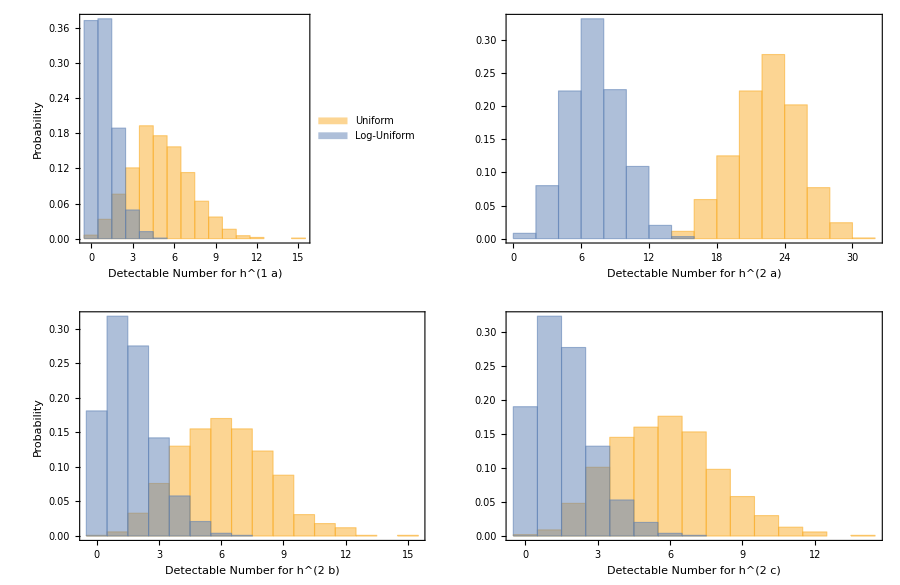

```mathematica
(*使用 GraphicsGrid 将图形按照 2 行 2 列进行排布*)
SNRCountHistPlot=GraphicsGrid[Partition[SNRCountHist,2],Spacings->{12,8},ImageSize->900]
Export[basePath <> "SNRCountHistAlpha10.eps",SNRCountHistPlot];
```

```mathematica
(*Uniform Sampling: save data for SNR>7*)
mergedSNRListsUniform=Table[{},{4}];
For[i=1,i≤4,i++,mergedSNRListsUniform[[i]]=Flatten[Table[newSNRListsUniform[[j,i]],{j,1,Nmcmc}]]]
Export[basePath <> "mergedSNRListsUniform.txt",mergedSNRListsUniform,"Table"];
```

```mathematica
(*Log-Uniform Sampling: save data for SNR>7*)
mergedSNRListsLogUniform=Table[{},{4}];
For[i=1,i≤4,i++,mergedSNRListsLogUniform[[i]]=Flatten[Table[newSNRListsLogUniform[[j,i]],{j,1,Nmcmc}]]]
Export[basePath <> "mergedSNRListsLogUniform.txt",mergedSNRListsLogUniform,"Table"];
```

```mathematica
(*import data using calculated results*)
mergedSNRListsUniform=Import[basePath <> "mergedSNRListsUniform.txt","Table"];
mergedSNRListsLogUniform=Import[basePath <> "mergedSNRListsLogUniform.txt","Table"];
```

```mathematica
(*Uniform Sampling: calculate medians and quantiles for SNR*)
mergedSNRListsUniformMedian=Median/@mergedSNRListsUniform;
mergedSNRListsUniformQuantile16=Quantile[#,{0.16}]&/@mergedSNRListsUniform;
mergedSNRListsUniformQuantile84=Quantile[#,{0.84}]&/@mergedSNRListsUniform;
Print["median for mergedSNRListsUniform：",mergedSNRListsUniformMedian]
Print["16% quantile for mergedSNRListsUniform：",mergedSNRListsUniformQuantile16]
Print["84% quantile for mergedSNRListsUniform：",mergedSNRListsUniformQuantile84]
```

median for mergedSNRListsUniform：{15.2692,30.1879,16.3158,16.4013}

16% quantile for mergedSNRListsUniform：{{8.67227},{11.1599},{8.80985},{8.86493}}

84% quantile for mergedSNRListsUniform：{{39.6318},{120.696},{49.2046},{50.1525}}

```mathematica
Flatten[mergedSNRListsUniformQuantile16]-mergedSNRListsUniformMedian
Flatten[mergedSNRListsUniformQuantile84]-mergedSNRListsUniformMedian
```

{-6.59694,-19.0279,-7.50595,-7.53632}

{24.3626,90.5083,32.8888,33.7513}

```mathematica
(*Log-Uniform Sampling: calculate medians and quantiles for SNR*)
mergedSNRListsLogUniformMedian=Median/@mergedSNRListsLogUniform;
mergedSNRListsLogUniformQuantile16=Quantile[#,{0.16}]&/@mergedSNRListsLogUniform;
mergedSNRListsLogUniformQuantile84=Quantile[#,{0.84}]&/@mergedSNRListsLogUniform;
Print["median for mergedSNRListsLogUniform：",mergedSNRListsLogUniformMedian]
Print["16% quantile for mergedSNRListsLogUniform：",mergedSNRListsLogUniformQuantile16]
Print["84% quantile for mergedSNRListsLogUniform：",mergedSNRListsLogUniformQuantile84]
```

median for mergedSNRListsLogUniform：{13.8293,20.8978,16.0913,16.1065}

16% quantile for mergedSNRListsLogUniform：{{8.34555},{9.59827},{8.82244},{8.88457}}

84% quantile for mergedSNRListsLogUniform：{{37.9417},{81.2532},{52.9273},{52.936}}

```mathematica
Flatten[mergedSNRListsLogUniformQuantile16]-mergedSNRListsLogUniformMedian
Flatten[mergedSNRListsLogUniformQuantile84]-mergedSNRListsLogUniformMedian
```

{-5.48371,-11.2995,-7.26883,-7.22195}

{24.1125,60.3554,36.8361,36.8295}

```mathematica
mergedSNRListsUniformQuantile95=Quantile[#,{0.95}]&/@mergedSNRListsUniform;
Print["90 upper quantile for mergedSNRListsUniform：",mergedSNRListsUniformQuantile95]
```

90 upper quantile for mergedSNRListsUniform：{{102.813},{319.423},{128.596},{130.083}}

```mathematica
(*检查每个列表的长度*)
isEmpty=Table[Length[mergedSNRListsUniform[[i]]],{i,1,4}]
isEmptyLog=Table[Length[mergedSNRListsLogUniform[[i]]],{i,1,4}]
```

{5032,21941,6156,5750}

{954,6713,1662,1616}

```mathematica
mergedSNRListsUniformSel=Map[ReplaceAll[#,x_/;x>10^5:>Null]&,mergedSNRListsUniform,{2}];
mergedSNRListsLogUniformSel=Map[ReplaceAll[#,x_/;x>10^5:>Null]&,mergedSNRListsLogUniform,{2}];
```

```mathematica
binBoundaries={3,8,4,4};
SNRDistHist=Table[Histogram[{mergedSNRListsUniformSel[[i]],mergedSNRListsLogUniformSel[[i]]},{binBoundaries[[i]]},"Probability",Frame->True,FrameStyle->Directive[Black,12],FrameLabel->{{If[Or[i==2,i==4],None,Style["Probability",Black,14,FontFamily->"Times New Roman"]],None},{Style["SNR for "<>labels[[i]],Black,17,FontFamily->"Times New Roman"],None}},ChartLegends->If[i==1,{Placed[{Style["Uniform",FontSize->15,FontFamily->"Times New Roman"],Style["Log-Uniform",FontSize->15,FontFamily->"Times New Roman"]},Scaled[{0.80,0.85}]]},None]],{i,1,4}];
```

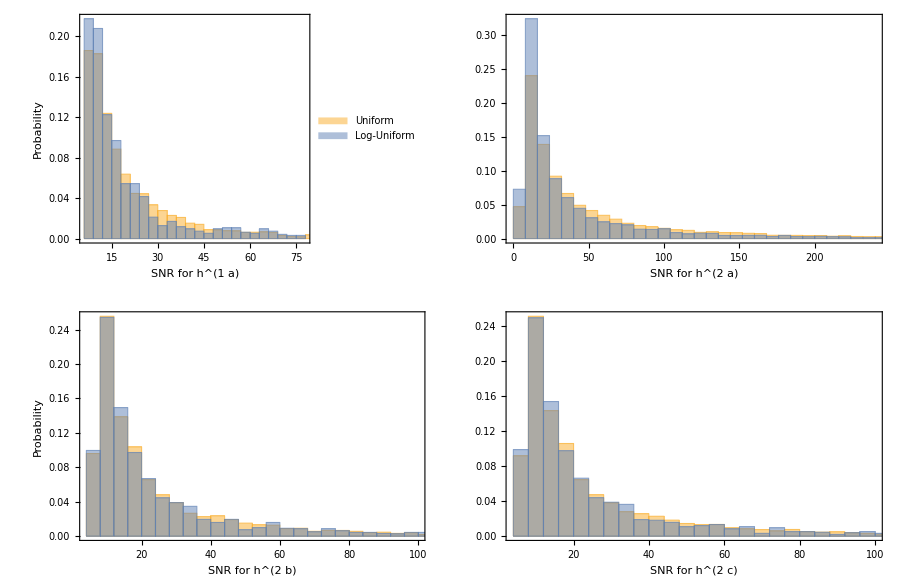

```mathematica
(*使用 GraphicsGrid 将图形按照 2 行 2 列进行排布*)
SNRDistHistPlot=GraphicsGrid[Partition[SNRDistHist,2],Spacings->{12,8},ImageSize->900]
Export[basePath <> "SNRDistHistAlpha10.eps",SNRDistHistPlot];
```

```mathematica
(*save data for ΔI3toI3*)
mergedΔI3toI3ListUniform=Flatten[ΔI3toI3ListUniform];
mergedΔI3toI3ListLogUniform=Flatten[ΔI3toI3ListLogUniform];
Export[basePath <> "mergedΔI3toI3ListUniform.txt",mergedΔI3toI3ListUniform,"Table"];
Export[basePath <> "mergedΔI3toI3ListLogUniform.txt",mergedΔI3toI3ListLogUniform,"Table"];
```

```mathematica
(*import data using calculated results*)
mergedΔI3toI3ListUniform=Import[basePath <> "mergedΔI3toI3ListUniform.txt","List"];
mergedΔI3toI3ListLogUniform=Import[basePath <> "mergedΔI3toI3ListLogUniform.txt","List"];
```

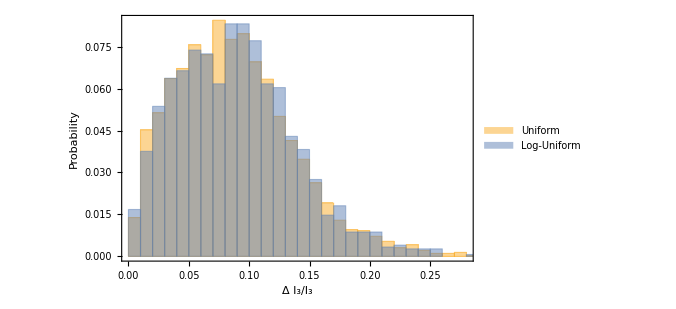

```mathematica
DeltaI3toI3Plot=Histogram[{mergedΔI3toI3ListUniform,mergedΔI3toI3ListLogUniform},Automatic,"Probability",Frame->True,FrameStyle->Directive[Black,14],FrameLabel->{{Style["Probability",Black,16,FontFamily->"Times New Roman"],None},{Style["Δ I_3/I_3",Black,20,FontFamily->"Times New Roman"],None}},ChartLegends->Placed[{Style["Uniform",FontSize->15,FontFamily->"Times New Roman"],Style["Log-Uniform",FontSize->15,FontFamily->"Times New Roman"]},Scaled[{0.80,0.85}]],ImageSize->500]
Export[basePath <> "DeltaI3toI3Alpha10.eps",DeltaI3toI3Plot];
```

```mathematica
(*Uniform Sampling: calculate medians and quantiles for ΔI3toI3*)
mergedΔI3toI3ListUniformMedian=Median[mergedΔI3toI3ListUniform];
mergedΔI3toI3ListUniformQuantile16=Quantile[mergedΔI3toI3ListUniform,{0.16}];
mergedΔI3toI3ListUniformQuantile84=Quantile[mergedΔI3toI3ListUniform,{0.84}];
Print["median for mergedΔI3toI3ListUniform：",mergedΔI3toI3ListUniformMedian]
Print["16% quantile for mergedΔI3toI3ListUniform：",mergedΔI3toI3ListUniformQuantile16]
Print["84% quantile for mergedΔI3toI3ListUniform：",mergedΔI3toI3ListUniformQuantile84]
```

median for mergedΔI3toI3ListUniform：0.0833569

16% quantile for mergedΔI3toI3ListUniform：{0.0382939}

84% quantile for mergedΔI3toI3ListUniform：{0.136609}

```mathematica
Flatten[mergedΔI3toI3ListUniformQuantile16]-mergedΔI3toI3ListUniformMedian
Flatten[mergedΔI3toI3ListUniformQuantile84]-mergedΔI3toI3ListUniformMedian
```

{-0.0450629}

{0.0532517}

```mathematica
(*Log-Uniform Sampling: calculate medians and quantiles for ΔI3toI3*)
mergedΔI3toI3ListLogUniformMedian=Median[mergedΔI3toI3ListLogUniform];
mergedΔI3toI3ListLogUniformQuantile16=Quantile[mergedΔI3toI3ListLogUniform,{0.16}];
mergedΔI3toI3ListLogUniformQuantile84=Quantile[mergedΔI3toI3ListLogUniform,{0.84}];
Print["median for mergedΔI3toI3ListLogUniform：",mergedΔI3toI3ListLogUniformMedian]
Print["16% quantile for mergedΔI3toI3ListLogUniform：",mergedΔI3toI3ListLogUniformQuantile16]
Print["84% quantile for mergedΔI3toI3ListLogUniform：",mergedΔI3toI3ListLogUniformQuantile84]
```

median for mergedΔI3toI3ListLogUniform：0.0870198

16% quantile for mergedΔI3toI3ListLogUniform：{0.0385048}

84% quantile for mergedΔI3toI3ListLogUniform：{0.136447}

```mathematica
Flatten[mergedΔI3toI3ListLogUniformQuantile16]-mergedΔI3toI3ListLogUniformMedian
Flatten[mergedΔI3toI3ListLogUniformQuantile84]-mergedΔI3toI3ListLogUniformMedian
```

{-0.048515}

{0.0494273}